```mathematica
ClearAll[r, x, y, z];
r0 = 1;
r[θ_, r0_] := r0 Sin[θ]^2;
x[θ_, φ_, r0_] := r[θ, r0] Sin[θ] Cos[φ];
y[θ_,  φ_, r0_] := r[θ, r0] Sin[θ] Sin[φ];
z[θ_,  φ_, r0_] := r[θ, r0] Cos[θ];
```

```mathematica
φ = π/4;
r0 = 1/4;
img = ParametricPlot3D[{
x[θ, φ, r0], y[θ, φ, r0], z[θ, φ, r0]
}, {θ, 0, 2π}, {φ, 0, 2π} ,
 PlotStyle->{Opacity[0.5], RGBColor[0, 0.7, 0]}, Boxed->False, Axes->False]
```

-Graphics3D-

```mathematica
path = "D:\\Kami\\git_folder\\notes_4sem\\field_theory\\homework\\figures\\"
Export[path<>"T13.pdf", img]
```

D:\Kami\git_folder\notes_4sem\field_theory\homework\figures\

D:\Kami\git_folder\notes_4sem\field_theory\homework\figures\T13.pdf

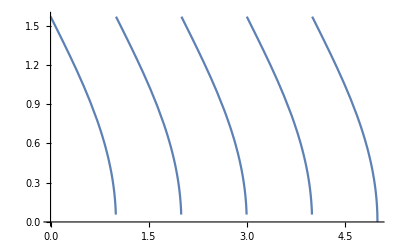

```mathematica
Plot[ArcCos[Mod[x, 1]], {x, 0, 5}, PlotRange->All]
```